# Лабораторная работа №4.

## Задание 1.

Создайте интерактивную панель для ввода пользователем концов двух отрезков с помощью мыши. Отобразите отрезки  красным цветом, если они пересекаются и зелёным в противном случае.

```mathematica
DynamicModule[{pointlist={}},Column[{Button["Refresh",pointlist={}],ClickPane[Framed@Dynamic@Graphics[{PointSize@0.02,Point/@pointlist,Black,Line/@Partition[pointlist,2]},PlotRange->{{0,10},{0,10}},ImageSize->500],AppendTo[pointlist,#]&]}]]
```

## Задание 2.

Создайте функцию, генерирующую итерации ковра серпинского. Фрактал задавайте списком точек. Отобразите точки на графической области.
Обеспечьте возможность просматривать накопление точек с помощью функции Manipulate или анимации.

```mathematica
base={{0,0},{0,1},{1,0},{1,1},{1/2,0},{1/2,1},{1,1/2},{0,1/2}}
```

{{0,0},{0,1},{1,0},{1,1},{1/2,0},{1/2,1},{1,1/2},{0,1/2}}

```mathematica
kover[base_,1]:=Flatten[{base,((base/3) [[#]]+{0,0/3})&/@Range[1,Length[base]],
((base/3) [[#]]+({0,1/3}))&/@Range[1,Length[base]],
((base/3) [[#]]+{0,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,1/3})&/@Range[1,Length[base]]},1]
kover[base_,n_]:=kover[Flatten[{base,((base/3) [[#]]+{0,0/3})&/@Range[1,Length[base]],
((base/3) [[#]]+({0,1/3}))&/@Range[1,Length[base]],
((base/3) [[#]]+{0,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,1/3})&/@Range[1,Length[base]]},1],n-1]
```

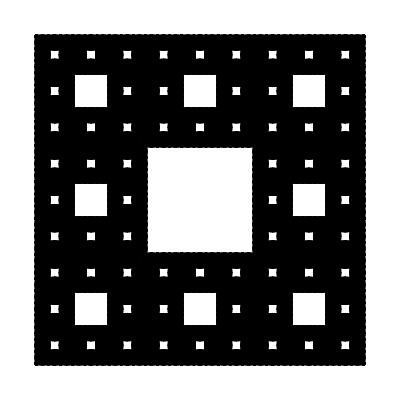

```mathematica
Graphics[{Point[kover[base,4]]}]
```

```mathematica
Manipulate[Graphics[Point[kover[base,a]]],{a,{1,2,3,4}}]
```

## Задание 3

1. Создайте игру, позволяющую пользователю бродить по сетке “целых точек” (точек с целыми координатами) в некоторой графической области. отобразите траекторию и количество сделанных шагов. Управление перемещением точки осуществляется с помощью кнопок. Предусмотрите невозможность выйти за пределы области, а также невозможность пересечения траектории. Предусмотрие кнопку для рестарта игры.
	2. Добавьте на поле специальную область (чёрный квадрат), после попадания в которую игра прекращается. Пользователь получает сообщение. И происходит рестарт.

```mathematica
DynamicModule[{pointlist={{10,10}},a=True},
Grid[
{
{Button["Up",AppendTo[pointlist,Last[pointlist]+{0,1}]],Button["Down",AppendTo[pointlist,Last[pointlist]+{0,-1}]]},{Button["left",AppendTo[pointlist,Last[pointlist]+{-1,0}]],Button["rigth",AppendTo[pointlist,Last[pointlist]+{1,0}]]},
{Dynamic@Graphics[
{Red,PointSize[0.02],Point[pointlist⟦-1⟧],Dashed,,Black,Line[pointlist]},
ImageSize->300,GridLines->{Range[1,20],Range[1,20]},GridLinesStyle->LightGray,Axes->True,PlotRange->{{0,20},{0,20}}
],SpanFromLeft}
},
ItemSize->{Scaled[0.15]}]]
```